R_1 and C_1 calculations

```mathematica
Clear[s];
c1=220*10^-9;
μ=1*10^-6;
m=1*10^-3;
fencmin=1μ;
fencmax=69.4m;
r1=47*10^3;
N[r1 c1 Log[3/2]]
```

0.00419251

## R_2 and C_2 calculations

## R_3 and C_3 calculations

```mathematica
j=I;
(*  H[jω]is Vout/Vin  *)
r3=100;
c3=47*10^-9;
```

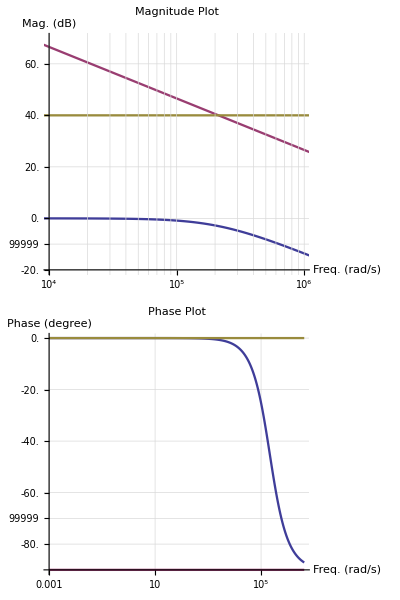

```mathematica
H[s_]:=1/(1+s r3 c3);
cap[s_]:=1/(s c3);
res = r3;
tf=BodePlot[{H[s],cap[s],res},GridLines->Automatic,Frame->False,
GridLinesStyle->LightGray,PlotLabel->{"Magnitude Plot","Phase Plot"},
PlotStyle->Thickness[0.003],
PlotRange->{{{10^4,10^6},{-20,70}},Automatic},
AxesLabel->{{"Freq. (rad/s)","Mag. (dB)"},{"Freq. (rad/s)","Phase (degree)"}},ImageSize->550]
```